# Analyzing time of flight data

## Prerequisites: sets constants, defines functions

### Constants

```mathematica
μB=9.27400915*10^-28;
kb=1.380658*10^-23;
ℏ=6.62606896*10^-34(2π)^-1;
c=299792458;
a0 = .529*10^-10;
ϵ0 = 8.854*10^-12;
el = 1.602*10^-19;
AMU=1.66*10^-27*kg;
cm=10^-2;mm=10^-3;μm=10^-6;nm = 10^-9;pm=10^-12;fm=10^-15;
kg=1;g=10^-3;ng=10^-9*g;pg=10^-12*g;
Hz=1;kHz=10^3;MHz=10^6;GHz=10^9; THz = 10^12;
Kk=1;mK=10^-3;μK=10^-6;nK=10^-9;
Ww=1;mW=10^-3;μW=10^-6;nW=10^-9;
Pa=1;GPa=10^9;
ms=10^-3;
ohm=1;V=1;mV=10^-3;
ns = 10^-9;
```

```mathematica
mass = 1.44*10^-25;
```

### Functions

```mathematica
convertToXY[set_ ] := (
dims =Dimensions[set];
dataXY=Flatten[Table[{i,j,Mean[set[[i,j]]]},{i,1,dims[[1]]},{j,1,dims[[2]]}],1]
);
```

```mathematica
fitData4[data_,xGuess_,yGuess_,wxGuess_,wyGuess_,ampGuess_]  :=(
dataXY = convertToXY[data];
(*θ=0;*)
fit= 
NonlinearModelFit[dataXY, offset+A*Exp[(-(x-x0)^2)/(2*σx^2)+(-(y-y0)^2)/(2*σy^2)],{{offset,0},{A,ampGuess},{x0,xGuess},{y0,yGuess},{σx,wxGuess},{σy,wyGuess}},{x,y}];
fit["ParameterTable"]
); (*performs 2d fit on the data*)
```

```mathematica
getFlourescence[image_,ROIx1_,ROIx2_,ROIy1_,ROIy2_]:=(
dataToFitTemp = image[[ROIx1;;ROIx2,ROIy1;;ROIy2]];
arrayList = Flatten[Table[Mean[dataToFitTemp[[i,j]]],{i,1,dims[[1]]},{j,1,dims[[2]]}],1];
flourCounts = Total[arrayList];
); (*returns the total number of counts in the data*)
```

```mathematica
fitDataSlices[data_,xBool_]  :=(
dataArray = Table[Mean[data[[i,j]]],{i,1,Dimensions[data][[1]]},{j,1,Dimensions[data][[2]]}];
dataToFit = If[xBool==1, Map[Total, Transpose[dataArray]], Map[Total, dataArray]];
xGuess =Position[dataToFit,Max[Flatten[dataToFit]]];
ampGuess=Max[Flatten[dataToFit]];
fit= 
NonlinearModelFit[dataToFit, offset+A*Exp[(-(x-x0)^2)/(2*σ^2)],{{offset,0},{A,ampGuess},{x0,xGuess[[1,1]]},{σ,30}},x];
Return[{σ/.fit["BestFitParameters"],x0/.fit["BestFitParameters"]}]
);(*performs 1d fit along an axis, the x-axis (y-axis) when xBool = 1 (≠1)*)
```

```mathematica
generateTOFData[images_,ROIx1_,ROIx2_,ROIy1_,ROIy2_]:=(
Clear[σxData,σyData];
dataList = {};
dataListPos = {};
correctCounter = 0;
wGuess = {30,30};
Do[
dataToFitTemp = images[[i]][[ROIx1;;ROIx2,ROIy1;;ROIy2]];
guess =Position[dataToFitTemp,Max[Flatten[dataToFitTemp]]];
ampGuess=Max[Flatten[dataToFitTemp]];
(*Print[guess];
dataToFit = dataToFitTemp[[guess[[1,1]]-25;;guess[[1,1]]+25,guess[[1,2]]-25;;guess[[1,2]]+25]];*)
dataToFit=dataToFitTemp;
fitData4[dataToFit,guess[[1,1]],guess[[1,2]], wGuess[[1]],wGuess[[2]],ampGuess];
If[fit["AdjustedRSquared"]>0.7,
dataPoint = {Abs[σx],Abs[σy]}/. fit["BestFitParameters"];
dataPointPos = {x0,y0}/. fit["BestFitParameters"];
If[Norm[dataPoint]<10000,wGuess=dataPoint];
AppendTo[dataList, {keyVals[[i]],dataPoint}];
AppendTo[dataListPos, {keyVals[[i]],dataPointPos}];
correctCounter=correctCounter+1;
];
Print[fit["AdjustedRSquared"]];,
{i,1,Length[images]}];
σxData =Map[{#[[1]]*10^-3,camScaleFactor*Abs[#[[2,1]]]}&, dataList];
σyData = Map[{#[[1]]*10^-3,camScaleFactor*Abs[#[[2,2]]]}&, dataList];
xPosData =Map[{#[[1]]*10^-3,camScaleFactor*Abs[#[[2,1]]]}&, dataListPos];
yPosData = Map[{#[[1]]*10^-3,camScaleFactor*Abs[#[[2,2]]]}&, dataListPos];
Print["Through out",Length[images]-correctCounter ," fits due to poor t-statistics"];
Return[{σxData,σyData}]
);(*when given a sequences of images, will fit all of the data, and collate it with the present assignemnt of keuy values. Take s awhile since it does 2D fits.*)
```

```mathematica
generateFlourData[images_,ROIx1_,ROIx2_,ROIy1_,ROIy2_]:=(
Clear[σxData,σyData];
dataList = {};
Do[
dataToFitTemp = images[[i]][[ROIx1;;ROIx2,ROIy1;;ROIy2]];
arrayList = Flatten[Table[Mean[dataToFitTemp[[i,j]]],{i,ROIx1,ROIx2},{j,ROIy1,ROIy2}],1];
flourCounts = Total[arrayList];
AppendTo[dataList, {keyVals[[i]],flourCounts}]
,{i,1,Length[images]}];
Return[dataList]
);(*when given a sequences of images, will extract total counts from all of the data, and collate it with the present assignemnt of keuy values.*)
```

```mathematica
fitTOFData[σxData_,σyData_]:=Module[{},
fitx = NonlinearModelFit[σxData, (√(σ0x^2+(σvx*t)^2)),  {{σ0x,.0005},{σvx,.1}}, t];
fity = NonlinearModelFit[σyData, √(σ0y^2+(σvy*t)^2), {{σ0y,.002},σvy}, t];
Return[{fitx,fity}]
];(*returns fit objects on TOF data (= spatial extent versus time, all in SI)*)
```

```mathematica
getTemperature[σv_] = Return[T = 1/kb mass*σv^2];
```

Return[0.0104298 σv^2]

## Set file location

```mathematica
SetDirectory["/Volumes/kaufman_heap/heap/180329/TOF2/"]
files = Drop[FileNames[],0];
images = Map[ImageData[Import[#,"bmp"]]&, files];
```

/Volumes/kaufman_heap/heap/180329/TOF2

## Extract TOF data and temperature

```mathematica
initVal = 1;
finVal =20;
```

```mathematica
numShots = Length[images];
keyFunc[index_]=initVal+(index-1)*(finVal-initVal)/numShots
rawKeys= ToExpression[ Map[StringSplit[StringSplit[#,"."][[1]],"_"][[2]]&,files]];
keyVals =Map[keyFunc,rawKeys];
```

1+19/20 (-1+index)

```mathematica
keyVals//N
```

{9.55,10.5,11.45,12.4,13.35,14.3,15.25,16.2,17.15,18.1,1.,19.05,1.95,2.9,3.85,4.8,5.75,6.7,7.65,8.6}

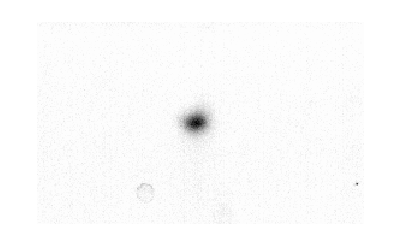

```mathematica
ArrayPlot[images[[1]], FrameTicks-> True]
```

```mathematica
initData = Sort[Transpose[{keyVals, images}]];
```

```mathematica
initData = Sort[Transpose[{keyVals, images}][[200;;420,400;;800]]];
```

$Aborted

```mathematica
σxListUncal = Map[{#[[1]],fitDataSlices[#[[2]],1][[1]]}&, initData];
σyListUncal = Map[{#[[1]],fitDataSlices[#[[2]],0][[1]]}&, initData];
```

```mathematica
xPosData = Map[{#[[1]],fitDataSlices[#[[2]],1][[2]]}&, initData];
yPosData = Map[{#[[1]],fitDataSlices[#[[2]],0][[2]]}&, initData];
```

FittedModel[27106.8 (0.00268376+5 t^2)]

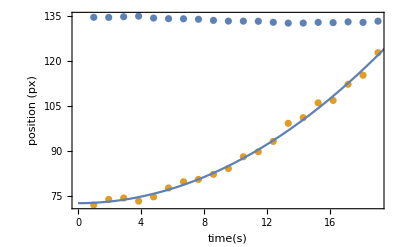

| Estimate | Standard Error | t-Statistic | P-Value
cal | 0.0000368911 | 6.11288×10^-7 | 60.3498 | 3.12789×10^-22
offset | 0.00268376 | 0.0000560705 | 47.8641 | 1.97919×10^-20

```mathematica
scaleFit=NonlinearModelFit[Map[{#[[1]]*ms,#[[2]]}&,Sort[yPosData]],cal^-1(1/2 10*t^2+offset),{cal,offset},t]

fp=Show[{ListPlot[{Map[{#[[1]],#[[2]]}&,Sort[xPosData]],Map[{#[[1]],#[[2]]}&,Sort[yPosData]]}],Plot[scaleFit[x*ms],{x,0,30}]}];
Show[fp, Frame-> True, Axes-> False, FrameLabel-> {"time(s)","position (px)"}]
scaleFit["ParameterTable"]
```

```mathematica
calibration = cal/.scaleFit["BestFitParameters"]
```

0.0000368911

```mathematica
σxData = Map[{#[[1]]*ms,#[[2]]calibration}&, σxListUncal];
σyData = Map[{#[[1]]*ms,#[[2]]calibration}&, σyListUncal];
```

```mathematica
σxData
```

{{1/1000,0.000287954},{39/20000,0.000279458},{29/10000,0.000276767},{77/20000,0.000276478},{3/625,0.000268946},{23/4000,0.000259464},{67/10000,0.000261894},{153/20000,0.000260466},{43/5000,0.000249148},{191/20000,0.000265083},{21/2000,0.000270436},{229/20000,0.000275092},{31/2500,0.000290596},{267/20000,0.000316695},{143/10000,0.000322446},{61/4000,0.000335337},{81/5000,0.00035706},{343/20000,0.000356443},{181/10000,0.00038253},{381/20000,0.000378133}}

```mathematica
σyData
```

{{1/1000,-0.000162613},{39/20000,-0.000165112},{29/10000,-0.000168759},{77/20000,-0.00017267},{3/625,-0.000172882},{23/4000,-0.000182672},{67/10000,-0.000188305},{153/20000,-0.000198967},{43/5000,-0.000224195},{191/20000,-0.000220886},{21/2000,-0.000230358},{229/20000,0.000232936},{31/2500,0.000253545},{267/20000,0.000276688},{143/10000,0.000279619},{61/4000,0.00027885},{81/5000,0.00030389},{343/20000,0.000299535},{181/10000,0.000334826},{381/20000,0.000372101}}

```mathematica
fits=fitTOFData[Abs[Sort[σxData]],Abs[Sort[σyData]]];
yTemp = getTemperature[σvy/.fits[[2]]["BestFitParameters"]];
xTemp = getTemperature[σvx/.fits[[1]]["BestFitParameters"]];
```

## Display data and temperature

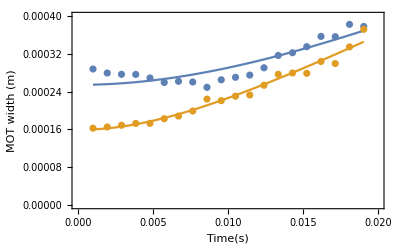

{T_x,T_y} = {0.00205796,0.0027073}mK

```mathematica
Show[{Plot[{fits[[1]][x],fits[[2]][x]}, {x,Min[keyVals]*ms,Max[keyVals]*ms}],ListPlot[{Abs[σxData],Abs[σyData]}]}, Frame-> True, Axes-> False, FrameLabel-> {"Time(s)", "MOT width (m)"}, PlotRange-> {{0,.02},{0,.4mm}}]
Print["{T_x,T_y} = {",xTemp/mK, ",", yTemp/mK,"}","mK"]
```

```mathematica
Export[]
```